### Categorization

Tutorial

PhysDataFetch

PhysDataFetch`

PhysDataFetch/tutorial/PhysDataFetch Tutorial

### Keywords

Details

# Importing data with PhysDataFetch

The PhysDataFetch package provides some utilities to fetch data useful for physicits.

IMPORTANT: This package is only an interface to some database. Make sure you properly cite them if you use them!

ESTARData | Fetch data from the ESTAR database, regarding electron passage through matter. PSTAR and ASTAR are also available for positron and alpha particle passage.
XRayData | Fetch data from the NIST X-Ray Mass Attenuation Coefficients [...] database.
XXXX | XXXX

XXXX.

Basic use.

```mathematica
Needs["PhysDataFetch`"]
```

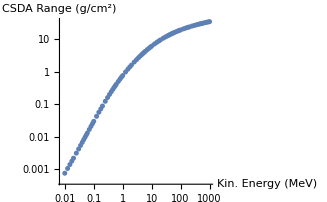

```mathematica
ListLogLogPlot[{ESTARData[74][[All,{1,5}]]},AxesLabel->{"Kin. Energy (MeV)","CSDA Range (g/cm^2)"}]
```

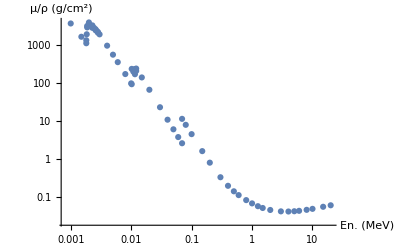

```mathematica
ListLogLogPlot[{XRayData[74][[All,{1,2}]]},AxesLabel->{"En. (MeV)","μ/ρ (g/cm^2)"}]
```

More About

Related Tutorials

Related Wolfram Education Group Courses